```mathematica
L=0.7;
S1=0.3  ;
S2=0.4 ;
```

If m_1,m_2>0 and m_1>m_2, then 0<σ_1<1.75

```mathematica
σ1=1.5   ; (*σ1=1.5*)
0<σ<1.75/.σ->σ1
```

True

### Parameter definitions

```mathematica
Δ1 = ((J^2-L^2-S1^2-S2^2)/2  -   SeffdL/σ2)/(σ1-σ2);
Δ2 = ((J^2-L^2-S1^2-S2^2)/2  -   SeffdL/σ1)/(σ1-σ2);
σ2 = 1+1/(-1+σ1)   ;

(*σ1=(1+ m2/m1)  σ2=(1+  m1/m2)*)
(* Not this σ1=(1+3/4 m2/m1)  σ2=(1+3/4  m1/m2)*)
```

### Cubic function roots

```mathematica
cubic =    Expand[ L^2 S1^2 S2^2- 2 σ1 σ2 (σ1-σ2)f(f-Δ1)(f-Δ2)-L^2(σ1-σ2)^2 f^2-S2^2 σ2^2(f-Δ1)^2-S1^2 σ1^2(f-Δ2)^2  ] (*The cubic polynomial of Eq. 3.1 of Cho-Lee*);
a3=Coefficient[cubic,f^3];
a2=Coefficient[cubic,f^2];
a1=Coefficient[cubic,f];
a0=Expand[cubic-(a3 f^3+a2 f^2+a1 f)];
p=(3 a1 a3-a2^2)/(3 a3^2);
q=(2 a2^3-9a1 a2 a3+27a0 a3^2)/(27 a3^3);
roots=Table[Subscript[f, k]->-a2/(3a3)+2 √(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-3/p)]+(2π k)/3],{k,1,3}];
f1=roots[[1,2]];
f2=roots[[2,2]];
f3=roots[[3,2]];
```

### Flow amounts definitions

```mathematica
(*The following definitions are in Cho-Lee*)
```

#### Δλ_(S_eff.L)

```mathematica
A=  2 σ1 σ2 (σ2-σ1) ;
β=√((f2-f1)/(f3-f1)) (*elliptic modulus "k"*);
Δλ1= 4/(√(A(f3-f1)))EllipticK[β];
```

#### Δλ_(J^2)

```mathematica
B1 = 1/2((SeffdL + L^2(σ1+σ2))(J+L)+ L(σ1 S1^2+σ2 S2^2+(σ1+σ2)(Δ2 σ1-Δ1 σ2))) ;
B2 = 1/2((SeffdL + L^2(σ1+σ2))(J-L)- L(σ1 S1^2+σ2 S2^2+(σ1+σ2)(Δ2 σ1-Δ1 σ2))) ;
D1=L(L+J)+Δ2 σ1-Δ1 σ2;
D2=L(L-J)+Δ2 σ1-Δ1 σ2;
α1 = ((σ1-σ2)(f2-f1))/(D1-f1(σ1-σ2))  ;
α2 = ((σ1-σ2)(f2-f1))/(D2-f1(σ1-σ2))  ;
Δλ2=-1/(2 J) (4/(√(A(f3-f1)))) ((B1  EllipticPi[α1,β^2])/(D1-f1(σ1-σ2))+(B2 EllipticPi[α2,β^2])/(D2-f1(σ1-σ2)));
```

#### Δλ_(L^2)

```mathematica
Δλ3=-1/(2 L)((4/(√(A(f3-f1)))) ((B1  EllipticPi[α1,β^2])/(D1-f1(σ1-σ2))-(B2 EllipticPi[α2,β^2])/(D2-f1(σ1-σ2)))  - (SeffdL +(Δ1-Δ2)σ1 σ2 + L^2(σ1+σ2))Δλ1/L )  ;
```

#### Δλ_(S_1^2)

```mathematica
B1S1= 1/2(-L^2 S1 σ1+J S1^2 σ1-S1^3 σ1-S1 Δ2 σ1^2+J^2 S1 σ2-2 J S1^2 σ2+S1^3 σ2-J Δ1 σ1 σ2+2 S1 Δ1 σ1 σ2+J Δ1 σ2^2-S1 Δ1 σ2^2)  ;
B2S1= 1/2(L^2 S1 σ1+J S1^2 σ1+S1^3 σ1+S1 Δ2 σ1^2-J^2 S1 σ2-2 J S1^2 σ2-S1^3 σ2-J Δ1 σ1 σ2-2 S1 Δ1 σ1 σ2+J Δ1 σ2^2+S1 Δ1 σ2^2)   ;
D1S1=-J S1+S1^2-Δ1 σ2;
D2S1=(J S1+S1^2-Δ1 σ2);

α1S1 = ((-σ1)(f2-f1))/(D1S1+f1 σ1)  ;
α2S1= ((-σ1)(f2-f1))/(D2S1+f1 σ1)  ;
Δλ4=-1/(2 S1)((4/(√(A(f3-f1))))(-(B1S1 EllipticPi[α1S1,β^2])/(D1S1+f1 σ1)+(B2S1 EllipticPi[α2S1,β^2])/(D2S1+f1 σ1))  +  S1(σ2-σ1)Δλ1  )  ;
```

#### Δλ_(S_2^2)

```mathematica
B1S2=1/2(S2 σ2(L^2-J S2+S2^2-Δ1 σ2)-(J-S2)^2 S2 σ1-(J-2S2)Δ2 σ1 σ2+(J-S2)Δ2 σ1^2);
B2S2=1/2(S2 σ2(-L^2-J S2-S2^2+Δ1 σ2)+(J+S2)^2 S2 σ1-(J+2S2)Δ2 σ1 σ2+(J+S2)Δ2 σ1^2);
D1S2=(J-S2)S2-Δ2 σ1;
D2S2=-(J+S2)S2-Δ2 σ1;
α1S2 = ((-σ2)(f2-f1))/(D1S2+f1 σ2)  ;
α2S2= ((-σ2)(f2-f1))/(D2S2+f1 σ2)  ;
Δλ5=-1/(2 S2)((4/(√(A(f3-f1))))(-(B1S2 EllipticPi[α1S2,β^2])/(D1S2+f1 σ2)+(B2S2 EllipticPi[α2S2,β^2])/(D2S2+f1 σ2))  +  S2(σ1-σ2)Δλ1  )  ;
```

### Fifth action J_5

```mathematica
I5=1/π(SeffdL Δλ1+J^2 Δλ2+L^2 Δλ3+S1^2 Δλ4+S2^2 Δλ5);
```

```mathematica
dI5=D[I5,SeffdL];
```

```mathematica
(*(*(*(*(*MinConst=NMinimize[{Abs[1/dI5],J>0,SeffdL>0},{SeffdL,J}]*)*)*)*)*)
```

### Spherical J_5

Assumming  along the  axis, thus

```mathematica
(*SeffdL=σ1 S1dL+σ2 S2dL*)
```

```mathematica
S1dL=S1 L(Cos[θ1] Cos[0]+Sin[θ1] Sin[0] Cos[ϕ1-0])
S2dL=S2 L(Cos[θ2] Cos[0]+Sin[θ2] Sin[0] Cos[ϕ2-0])
S1dS2=S1 S2(Cos[θ1] Cos[θ2]+Sin[θ1] Sin[θ2] Cos[Δϕ])
```

0.21 Cos[θ1]

0.28 Cos[θ2]

0.12 (Cos[θ1] Cos[θ2]+Cos[Δϕ] Sin[θ1] Sin[θ2])

```mathematica
dI5sph=dI5/.{SeffdL->(σ1 S1dL+σ2 S2dL)}/.{J->√(L^2+S1^2+S2^2+2(S1dL+S2dL+S1dS2))};
```

```mathematica
MinAngles=NMinimize[{Abs[1/dI5sph],0<=θ1<= π, 0<=θ2<=   π, 0<=Δϕ<=2 π   (*,(σ1 S1dL+σ2 S2dL)>0*)     },{θ1,θ2,Δϕ}, WorkingPrecision->10, PrecisionGoal->10]
```

{4.52114214×10^-8,{θ1→0.9890216444,θ2→1.579368912,Δϕ→6.283179773}}

```mathematica
Jphys=√(L^2+S1^2+S2^2+2(S1dL+S2dL+S1dS2))//.MinAngles[[2]]
```

1.07952

```mathematica
SeffdLphys=(σ1 S1dL+σ2 S2dL)//.MinAngles[[2]]
```

0.165894

```mathematica
Re[1/dI5/.J->Jphys]/.SeffdL->SeffdLphys
Im[1/dI5/.J->Jphys]/.SeffdL->SeffdLphys
```

4.5208×10^-8

0

```mathematica
plot3D =Plot3D[Abs[1/dI5] , {J,0.97Jphys, 1.03 Jphys} , {SeffdL , 0.9 SeffdLphys, 1.1 SeffdLphys}]
```

-Graphics3D-

```mathematica
MinAngles[[2]]
```

{θ1→0.9890216444,θ2→1.579368912,Δϕ→6.283179773}

```mathematica
MinAnglesPert = {θ1->0.96 0.98902164442463530490415386700357927224`10.,θ2->1.008 1.5793689119644163280527142220488544371`10.,Δϕ-> 1.06 6.2831797725274802968`10.};
JphysPert=√(L^2+S1^2+S2^2+2(S1dL+S2dL+S1dS2))//.MinAnglesPert 
SeffdLphysPert=(σ1 S1dL+σ2 S2dL)     //.MinAnglesPert 

verticalLine1=Graphics3D[{Red,Thickness[0.007],Line[{{Jphys,SeffdLphys,-6},{Jphys,SeffdLphys,6}}] }];
verticalLine2=Graphics3D[{Blue,Thickness[0.007],Line[{{JphysPert,SeffdLphysPert,-6},{Jphys,SeffdLphysPert,6}}] }];
Show[plot3D,verticalLine1,verticalLine2]
```

1.07287

0.165555

-Graphics3D-

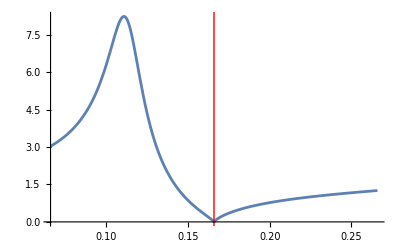

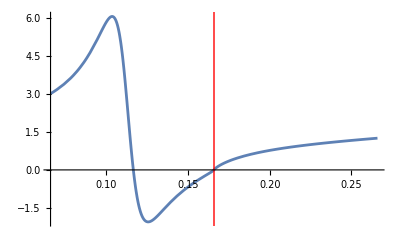

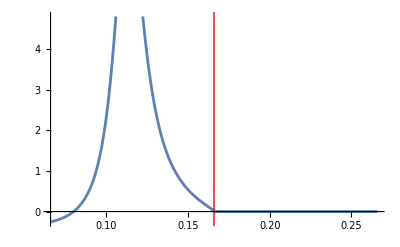

```mathematica
lowLim = SeffdLphys - 0.1; upLim = SeffdLphys + 0.1;
Plot[Abs[1/dI5]/. J->Jphys,{SeffdL,lowLim,upLim},Epilog->{Red,Line[{{SeffdLphys,-10^6},{SeffdLphys,10^6}}]}]
Plot[Re[1/dI5]/. J->Jphys,{SeffdL,lowLim,upLim},Epilog->{Red,Line[{{SeffdLphys,-10^6},{SeffdLphys,10^6}}]}]
Plot[Im[1/dI5]/. J->Jphys,{SeffdL,lowLim,upLim},Epilog->{Red,Line[{{SeffdLphys,-10^6},{SeffdLphys,10^6}}]}]
```

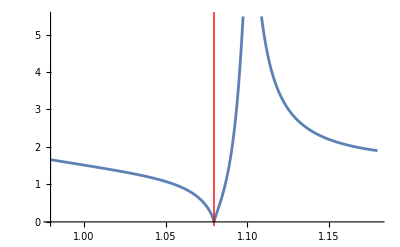

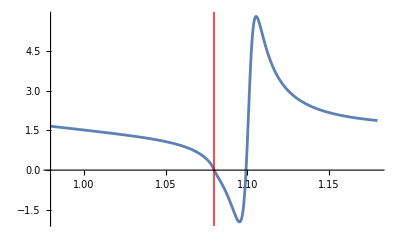

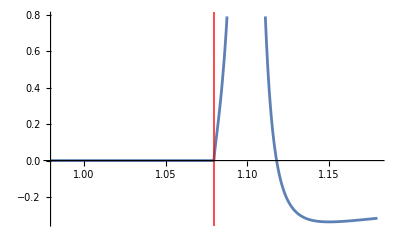

```mathematica
lowLim = Jphys - 0.1; upLim = Jphys + 0.1;
Plot[Abs[1/dI5]/. SeffdL->SeffdLphys,{J,lowLim,upLim},Epilog->{Red,Line[{{Jphys,-10^6},{Jphys,10^6}}]}]
Plot[Re[1/dI5]/. SeffdL->SeffdLphys,{J,lowLim,upLim},Epilog->{Red,Line[{{Jphys,-10^6},{Jphys,10^6}}]}]
Plot[Im[1/dI5]/. SeffdL->SeffdLphys,{J,lowLim,upLim},Epilog->{Red,Line[{{Jphys,-10^6},{Jphys,10^6}}]}]
```

```mathematica
Roots1=roots/.J->Jphys/.SeffdL->SeffdLphys
Roots2=roots/.J->JphysPert/.SeffdL->SeffdLphysPert
```

{f_1→-0.0664603,f_2→-0.0664597,f_3→0.163268}

{f_1→-0.0773417,f_2→-0.0477962,f_3→0.164806}

### Spherical to cartesian

```mathematica
CartesianVector[r_,θ_,ϕ_]:={r Sin[θ] Cos[ϕ],r Sin[θ] Sin[ϕ],r Cos[θ]};
RotateVectorAroundAxis[L_,S_,phi_]:=Module[{SUnit,LParallel,LPerpendicular,RotationMatrix,LFinal},
SUnit=Normalize[S];
LParallel=(Dot[L,SUnit]) SUnit;
LPerpendicular=L-LParallel;
RotationMatrix=RotationTransform[phi,SUnit];
LFinal=LParallel+RotationMatrix[LPerpendicular];
LFinal];
```

```mathematica
S10=CartesianVector[S1,θ1,ϕ1]/.ϕ1->0/.MinAngles[[2]];
S20=CartesianVector[S2,θ1,ϕ2]/.ϕ2->ϕ1-Δϕ/.ϕ1->0/.MinAngles[[2]];
L0=CartesianVector[L,0,0]
J0=L0+S10+S20;
```

{0.,0.,0.7}

### Vector rotation & perturbation

```mathematica
L1=RotateVectorAroundAxis[L0,S10+S20,0.01]
J1=L1+S10+S20;
```

{0.0000160871,-0.00584832,0.699976}

### System equations

```mathematica
Clear[S1,S2,L]
```

Recall that m_1>m_2

```mathematica
d=1;
m1 = 1;
m2 = 1/2 ;  
M=m1+m2;
μ =  (m1 m2)/M ;
q = m1/m2 ;
```

```mathematica
dS1[t_] =   1/(2 d^3) Cross[(4 + 3 m2/m1 - 3 μ/m1( ((1+m2/m1)L[t].S1[t]+(1+m1/m2)L[t].S2[t])/Norm[L[t]]^2))L[t]+S2[t], S1[t]] ;
dS2[t_] =    1/(2 d^3) Cross[(4 + 3 m1/m2 - 3 μ/m2 ( ((1+m2/m1)L[t].S1[t]+(1+m1/m2)L[t].S2[t])/Norm[L[t]]^2))L[t]+S1[t], S2[t]] ;
dL[t_]= 1/(2 d^3) Cross[ (S1[t]+S2[t]) +3 (1-μ/M( ((1+m2/m1)L[t].S1[t]+(1+m1/m2)L[t].S2[t])/Norm[L[t]]^2))((1+m2/m1)S1[t]+(1+m1/m2)S2[t]), L[t]] ;
```

```mathematica
sol0=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , L'[t]==dL[t],S1[0]==S10,S2[0]==S20, L[0]==L0  },   {S1,S2,L},{t,0,30}];
sol1=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , L'[t]==dL[t],S1[0]==S10,S2[0]==S20, L[0]==L1  },   {S1,S2,L},{t,0,30}];
```

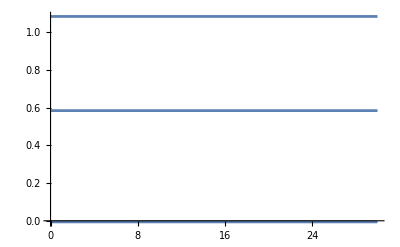

```mathematica
Plot[Evaluate[L[t]+S1[t]+S2[t]/.sol1[[1]]],{t,0,30}]
```

```mathematica
ξ0=1/M^2 Dot[((1+1/q)S10+(1+q)S20),L0/Norm[L0]]
ξ1=1/M^2 Dot[((1+1/q)S10+(1+q)S20),L1/Norm[L1]]
```

0.402972

0.402972

```mathematica
normrules={J->Norm[J0],L->Norm[L0],S1->Norm[S10],S2->Norm[S20]}//N
```

{J→1.23228,L→0.7,S1→0.3,S2→0.4}

```mathematica
J>S1+S2-L//.normrules
Smin=Max[Abs[J-L],Abs[S1-S2]]//.normrules
Smax=Min[J+L,S1+S2]//.normrules
```

True

0.532281

0.7

```mathematica
ξmax=1/(4 L M^2 q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.S->Smin
ξmin=1/(4 L M^2  q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.S->Smax
```

0.488445

0.366338

```mathematica
NormS0[t_]:=Norm[(S1/.sol0[[1]])[t]+(S2/.sol0[[1]])[t]];
NormS1[t_]:=Norm[(S1/.sol1[[1]])[t]+(S2/.sol1[[1]])[t]];
```

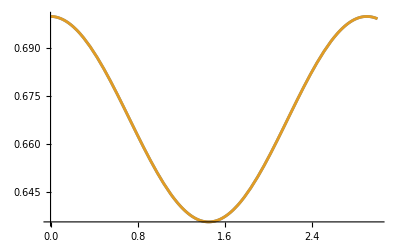

```mathematica
Plot[{NormS0[t],NormS1[t]},{t,0,3}]
```

```mathematica
ContξSp=1/(4 L M^2 q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.Cos[ϕ]->-1//FullSimplify
ContξSm=1/(4 L M^2 q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.normrules/.Cos[ϕ]->+1//FullSimplify
```

(-0.017142+0.751322 S^2-0.714286 S^4-0.238095 √(1.02852-1. (-1.4+S) S) √(-0.0049+0.5 S^2-1. S^4) √(-1.02852+S (1.4+S)))/S^2

(-0.017142+0.751322 S^2-0.714286 S^4+0.238095 √(1.02852-1. (-1.4+S) S) √(-0.0049+0.5 S^2-1. S^4) √(-1.02852+S (1.4+S)))/S^2

```mathematica
TheEgg=RegionPlot[{ξ<ContξSm&&ξ>ContξSp&&ξ<ξmax,ξ<ContξSm&&ξ>ContξSp&&ξ>ξmax,ξ<ContξSm&&ξ>ContξSp&&ξmin<ξ<ξmax},{S,Smin,Smax},{ξ,ξmin-0.1,ξmax+0.1},PlotRange->{All,All},ImageSize->Large];
```

```mathematica
Manipulate[Show[TheEgg,Graphics[{PointSize[0.015],Black,Point[{NormS0[t],ξ0}]}],Graphics[{PointSize[0.015],Purple,Point[{NormS1[t],ξ1}]}],PlotRange->All,Frame->True,FrameLabel->{Style["S(t)",15,Black],Style["ξ",15,Black]},FrameStyle->Directive[15,Black]],{t,0,0.5}]
```

```mathematica
A1=(J^2-(L-S)^2)^(1/2);
A2=((L+S)^2-J^2)^(1/2);
A3=(S^2-(S1-S2)^2)^(1/2);
A4=((S1+S2)^2-S^2)^(1/2);
```

```mathematica
Simplify[((J^2-L^2-S^2)(S^2(1+q)^2-(S1^2-S2^2)(1-q^2))-(1-q^2)A1 A2 A3 A4 Cos[ϕ])/(4q M^2 S^2 L)/.S1->Norm[S10]/.S2->Norm[S20]/.L->Norm[L0]/.J->Norm[J0]]
```

(-0.017142+0.751322 S^2-0.714286 S^4+0.238095 √(1.02852+1.4 S-S^2) √(-1.02852+1.4 S+S^2) √(-0.0049+0.5 S^2-1. S^4) Cos[ϕ])/S^2

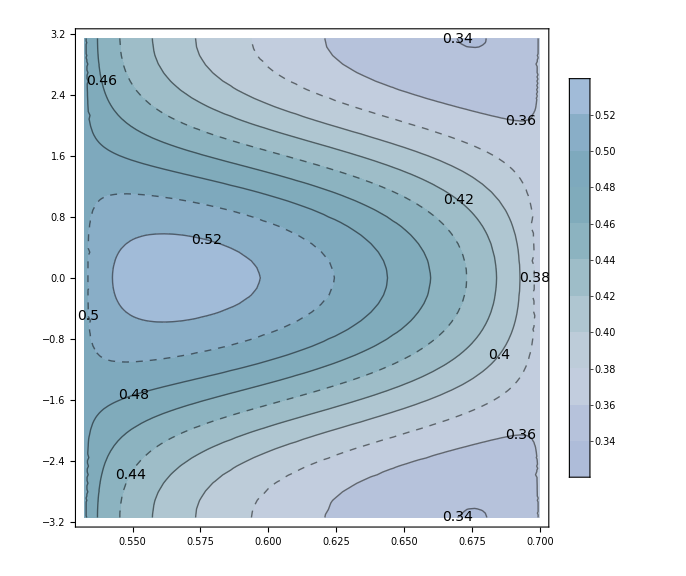

```mathematica
ContourPlot[1/S^2(-0.017141956299297868+0.7513219366365744 S^2-0.7142857142857142 S^4+0.23809523809523805 √(1.028517377957871+1.4 S-S^2) √(-1.028517377957871+1.4 S+S^2) √(-0.004900000000000008+0.49999999999999994 S^2-1. S^4) Cos[ϕ]),{S,Smin,Smax},{ϕ,-π,π},FrameLabel->{Style["",16],Style["",16]},ContourLabels->(Text[Style[#3,14],{#1,#2},Background->LightYellow]&),PlotLegends->Automatic,ColorFunction->"Aquamarine",ContourStyle->{Black,Black,Dashed},ImageSize->Large]
```

```mathematica
S1V0[t_]:=(S1/.sol0[[1]])[t]
S2V0[t_]:=(S2/.sol0[[1]])[t]
LV0[t_]:=(L/.sol0[[1]])[t]
JV0[t_]:=LV0[t]+S1V0[t]+S2V0[t]
SV0[t_]:=S1V0[t]+S2V0[t]
```

```mathematica
S1u0[t_]:=S1V0[t]/Norm[S1V0[t]];
Su0[t_]:=SV0[t]/Norm[SV0[t]];
```

```mathematica
zcapZ[t_]:=JV0[t]/Norm[JV0[t]]
xcapX[t_]:=(LV0[t]-(Dot[LV0[t],zcapZ[t]]zcapZ[t]))/Norm[LV0[t]-(Dot[LV0[t],zcapZ[t]]zcapZ[t])]
ycapY[t_]:=Cross[zcapZ[t],xcapX[t]]
```

```mathematica
SO10[t_]:=Cross[ycapY[t],SV0[t]];
SOu0[t_]:=SO10[t]/Norm[SO10[t]];
cosϕ10[t_]:=Dot[S1u0[t],SOu0[t]]/Norm[Cross[S1u0[t],Su0[t]]];
```

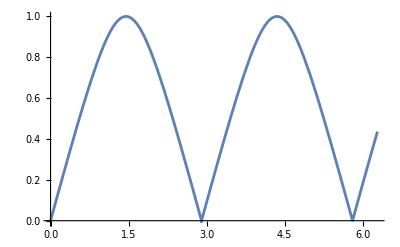

```mathematica
Plot[cosϕ10[t],{t,0,2π}]
```